### Basic Check

is it normalized

```mathematica
FullSimplify[(Sum[(λ^(2(n+m))),{n,0,∞},{m,0,∞}])^2(1-λ^2)^4 ,Assumptions->{λ∈Reals}]
```

1

```mathematica
modeOcc=FullSimplify[(1-λ^2)^2 Sum[n λ^(2(n+m)),{n,0,∞},{m,0,∞}],Assumptions->{λ∈Reals,λ>0}]
```

λ^2/(1-λ^2)

```mathematica
lambdaGivenNanyroot=InverseFunction[modeOcc/.λ->#&]
lambdaGivenN[x_]=Abs[lambdaGivenNanyroot[x]]
SameQ[0.1,modeOcc/.(λ->lambdaGivenN[0.1])]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-(√#1)/(√(1+#1))&

Abs[(√x)/(√(1+x))]

True

Finding g^(2) using the truncated formula

```mathematica
p1=Simplify[(1-λ^2)^2 Sum[(λ^(n+1)) ,{n,0,∞}]^2]
p2=Simplify[(1-λ^2)^2 Sum[(λ^(n+2)) ,{n,0,∞}]^2]
px=Simplify[(1-λ^2)^2 Sum[(λ^(n+x)) ,{n,0,∞}]^2]
Print["g^2 at low mode occupation P(x)=0 when x>0"]
g2simple=(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)
g2simple/.{λ->0.01}
Print["g^2 limit at no mode occupancy"]
Limit[g2simple,λ->0]
```

λ^2 (1+λ)^2

λ^4 (1+λ)^2

λ^(2 x) (1+λ)^2

g^2 at low mode occupation P(x)=0 when x>0

(2 λ^4 (1+λ)^2)/((λ^2 (1+λ)^2+2 λ^4 (1+λ)^2)^2)

1.95981

g^2 limit at no mode occupancy

2

```mathematica
g2full=Sum[n(n-1)(px/.{x->n}),{n,0,∞}]/Sum[n(px/.{x->n}),{n,0,∞}]^2
```

-(2 (-1+λ))/(1+λ)

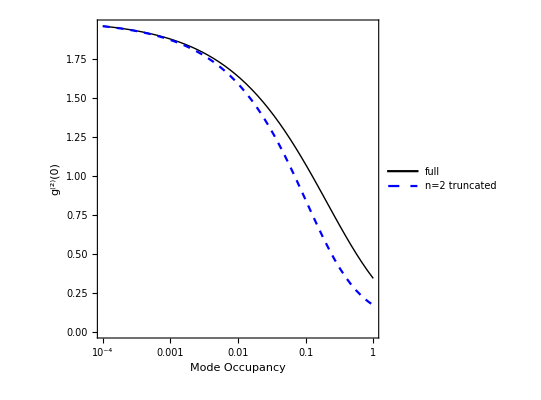

```mathematica
LogLinearPlot[{g2full/.{λ->lambdaGivenN[x]},g2simple/.{λ->Abs[lambdaGivenN[x]]}},{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"full","n=2 truncated"},Center],PlotStyle->{{Black,Thick},{Blue,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","g^(2)(0)"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

## Finding Coincidences

Find the noncoincident output state probability

```mathematica
ProbZeroX=(1-λ^2)Sum[λ^(m+n)1/(Factorial[m]Factorial[n])(1/2)^(m+n)ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))
				Sum[ⅈ^(-j+k)ⅇ^(ⅈ ϕ(-j-k))
					Binomial[m,j]Binomial[n,k]
					√(Factorial[m+n-j-k]Factorial[j+k])
					KroneckerDelta[m+n-j-k]KroneckerDelta[j+k-X]
					,{j,0,n},{k,0,m}]
				Sum[ⅈ^(-a+b)ⅇ^(ⅈ ϕ(a-b))
					Binomial[m,a]Binomial[n,b] 
					√(Factorial[m+n-a-b]Factorial[a+b])
					KroneckerDelta[m+n-a-b]KroneckerDelta[a+b-X] 
					,{a,0,n},{b,0,m}]
,{m,0,∞},{n,0,∞}]
```

$Aborted

```mathematica
Factorial[0]
```

1

```mathematica
Sum[ⅈ^(-j+k)ⅇ^(ⅈ ϕ(-j-k))Binomial[m,j]Binomial[n,k]
					√(Factorial[m+n-j-k]Factorial[j+k])
					KroneckerDelta[m+n-j-k]KroneckerDelta[j+k-X]
					,{j,0,n},{k,0,m}]
```

$Aborted

The simplified version

```mathematica
ProbZeroX=((1-λ^2)(1/2)^X λ^(X)(Factorial[X])ⅈ^(2X)ⅇ^(-2 ⅈ ϕ X) Sum[1/(Factorial[m]Factorial[n])ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))
				Sum[ⅈ^(-2j)
					Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
				Sum[ⅈ^(-2a)
					Binomial[m,a]Binomial[X-m,X-a]
					,{j,0,X-m}]
,{m,0,X}])^2
```

$Aborted

```mathematica
ⅈ^(-2x)-(-1)^x/.{x->{-1,0,1,2,3,4,5}}
ⅈ^(2x)-(-1)^x/.{x->{-2,-1,0,1,2,3,4,5}}
```

{0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

```mathematica
FullSimplify[(-1)^(2m),Assumptions->{m∈Integers}]
```

1

```mathematica
FullSimplify[Binomial[m,j]Binomial[X-m,X-j],Assumptions->Assumptions->{m∈Integers,X∈Integers,j∈Integers}]
```

Binomial[m,j] Binomial[-m+X,-j+X]

```mathematica
Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
```

∑_(j=0)^m (-1)^j Binomial[m,j] Binomial[-m+X,-j+X]

```mathematica
numinnersum[y_]:=NSum[(-1)^j Binomial[y,j]Binomial[X-y,X-j]
					,{j,0,y},Method->"AlternatingSigns",PrecisionGoal->30,AccuracyGoal->20]
numinnersum[10]
```

1.

```mathematica
Table[numinnersum[x]-(-1)^x,{x,0,30}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-4.57001×10^-12,7.02506×10^-11,-8.7832×10^-10,9.07612×10^-9,-7.8543×10^-8,5.7547×10^-7,-3.60273×10^-6}

```mathematica
Simplify[Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m-1}]+
Sum[(-1)^j Binomial[m,j]Binomial[X-m,X-j]
					,{j,m,m}],Assumptions->m∈Integers]
```

0

```mathematica
IsOdd[X_]=Piecewise[{{1,Mod[X,2]==1}},0]
Map[IsOdd,{0,1,2,3}]
```

Piecewise[{{1, Mod[X,2]==1}, {0, True}}]

{0,1,0,1}

```mathematica
Sum[(-1)^j(5+j^3),{j,0,X}]/.X->{1,2,3,4,5}
Table[Sum[5+(2j)^3,{j,0,((X-IsOdd[X])/2)}]-Sum[5+(2j+1)^3,{j,0,((X-IsOdd[X])/2)-1+IsOdd[X]  }]/.X-> Y,{Y,{1,2,3,4,5}}]
```

{-1,12,-20,49,-81}

{-1,12,-20,49,-81}

```mathematica
Sum[(-1)^j(5+j^3.2),{j,0,5}]
Sum[5+(2j)^3.2,{j,0,(5-1)/2}]-Sum[5+(2j+1)^3.2,{j,0,((5-1)/2)}]
```

-113.463

-113.463

```mathematica
EvenQ[2]
```

True

```mathematica
Sum[Binomial[m,2j]Binomial[X-m,X-2j]
					,{j,0,m/2}]
Sum[Binomial[m,2j]Binomial[X-m,X-2j]
					,{j,0,(m/2-1) }]
```

1/2 ((1-X)^m+(-1+X)^m) (1-X)^-m

-1+((2-3 m+m^2) Binomial[-m+X,-2+X] (√π Gamma[X]-Gamma[X/2] Gamma[(1+X)/2]))/((-1+X) X Gamma[X/2] Gamma[(1+X)/2])+(-1+m) Binomial[-m+X,-2+X] HypergeometricPFQ[{1-m/2,1-X/2,3/2-X/2},{3/2,2-m/2},1]

```mathematica
Sum[(-1)^m Binomial[m,j]Binomial[X-m,X-j]
					,{j,0,m}]
```

(-1)^m

```mathematica
FullSimplify[ⅈ^(-2x)-(-1)^x,Assumptions->X∈Integers]
```

-2 ⅈ Sin[π x]

```mathematica
({Binomial[-m+X,X]^2 ,Hypergeometric2F1[-m,-X,1-m,-1]^2}
)/.m->1
```

{0,ComplexInfinity}

```mathematica
Sum[1/(Factorial[m]Factorial[X-m])ⅈ^(2m)ⅇ^(ⅈ ϕ(2m))innersum,{m,1,2}]
```

Infinity::indet: Indeterminate expression 0 ⅈ^(2 X) ComplexInfinity encountered.

Indeterminate

```mathematica
ProbZeroX=FullSimplify[(Abs[(1-λ^2)(1/2)^X λ^(X)(Factorial[X])ⅇ^(-2 ⅈ ϕ X) Sum[1/(Factorial[m]Factorial[X-m])(-1)^m ⅇ^(ⅈ ϕ(2m)),{m,0,X}]])^2,Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
```

4^-X Abs[(λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2)]^2

```mathematica
ProbZeroX=FullSimplify[4^-X ((λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2))((λ-ⅇ^(-2 ⅈ ϕ) λ)^X (-1+λ^2)),Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
```

(-1+λ^2)^2 (λ^2 Sin[ϕ]^2)^X

```mathematica
ProbNoAtoms=(1-λ^2)^2
```

(1-λ^2)^2

```mathematica
(2ProbZeroX)/(1-ProbNoAtoms)/.{X->1,ϕ->0,λ->0.001}
```

0.25

```mathematica
ProbClickZero=FullSimplify[Sum[ProbZeroX,{X,1,∞}],Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
ClickNcoProb=(2ProbClickZero+ProbNoAtoms)
ClickNcoProb/.{λ->lambdaGivenN[0.1],ϕ->0.2}
```

-(λ^2 (-1+λ^2)^2 Sin[ϕ]^2)/(-1+λ^2 Sin[ϕ]^2)

(1-λ^2)^2-(2 λ^2 (-1+λ^2)^2 Sin[ϕ]^2)/(-1+λ^2 Sin[ϕ]^2)

0.832398

(1-λ^2)^2

```mathematica
ProbNoAtoms/.λ->0.1
ProbClickZero/.λ->0.1
```

0.9801

-(0.009801 (-1+ⅇ^(2 ⅈ ϕ))^2)/(-3.99-0.02 ⅇ^(2 ⅈ ϕ)+0.01 ⅇ^(4 ⅈ ϕ))

(1-λ^2)^2+2 (-1+λ^2)^2 (BesselI[0,λ]+BesselI[0,2 λ]-2 BesselI[0,√2 λ])

### Numerical sum

```mathematica
ProbClickZeroNum[λin_,ϕin_]:=Sum[ProbZeroXNumV2[xvar,λin,ϕin],{xvar,1,10}]
ClickNcoProbNum[λin_,ϕin_]:=(2ProbClickZeroNum[λin,ϕin]+ProbNoAtoms/.{λ->λin})
1-ClickNcoProbNum[0.1,π/4]
1-ClickNcoProbDist/.λ->0.1
```

0.019851

0.000149999

```mathematica
ProbZeroXNumV2[Xin_,λin_,ϕin_]:=Abs[(1-λin^2)(1/2)^Xin λin^Xin ParallelSum[1/(Factorial[m]Factorial[(Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-j+k)ⅇ^(ⅈ ϕin(-j-k))
					Binomial[m,j]Binomial[(Xin-m),k]
					√(Factorial[Xin-j-k]Factorial[j+k])
					KroneckerDelta[Xin-j-k]KroneckerDelta[j+k-Xin]
					)
				(ⅈ^(-a+b)ⅇ^(ⅈ ϕin(-a-b))
					Binomial[m,a]Binomial[Xin-m,b] 
					√(Factorial[Xin-a-b]Factorial[a+b])
					KroneckerDelta[Xin-a-b]KroneckerDelta[a+b-Xin] 
					)
,{m,0,Xin},{j,0,m},{k,0,(Xin-m)},{a,0,m},{b,0,(Xin-m)}]]^2
Table[ProbZeroXNumV2[xin,0.1,π/4],{xin,0,5}]
Table[ProbZeroX/.{X->xin,λ->0.1,ϕ->π/4},{xin,0,5}]
```

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

{0.9801+0. ⅈ,0.0049005+0. ⅈ,0.0000245025+0. ⅈ,1.22513×10^-7+0. ⅈ,6.12563×10^-10+0. ⅈ,3.06281×10^-12+0. ⅈ}

```mathematica
ProbZeroXNumV3[Xin_,λin_,ϕin_]:=Abs[(1-λin^2)(1/2)^Xin λin^Xin ⅈ^(2 Xin)Factorial[Xin]ParallelSum[1/(Factorial[m]Factorial[(Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-2j)ⅇ^(ⅈ ϕin(-Xin))
					Binomial[m,j]Binomial[(Xin-m),(Xin-j)]
					)
				(ⅈ^(-2a)ⅇ^(ⅈ ϕin(-Xin))
					Binomial[m,a]Binomial[Xin-m,(Xin-a)] 
					)
,{m,0,Xin},{j,0,m},{a,0,m}]]^2
Table[ProbZeroXNumV3[xin,0.1,π/4],{xin,0,5}]
Table[ProbZeroX/.{X->xin,λ->0.1,ϕ->π/4},{xin,0,5}]
```

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

{0.9801+0. ⅈ,0.0049005+0. ⅈ,0.0000245025+0. ⅈ,1.22513×10^-7+0. ⅈ,6.12563×10^-10+0. ⅈ,3.06281×10^-12+0. ⅈ}

```mathematica
ProbZeroXNumV4[Xin_,λin_,ϕin_]:=Abs[(1-λin^2)(1/2)^Xin λin^Xin ⅈ^(2 Xin)Factorial[Xin] ⅇ^(ⅈ ϕin(-2Xin))ParallelSum[1/(Factorial[m]Factorial[(Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(-1)^m
				((-1)^a
					Binomial[m,a]Binomial[Xin-m,(Xin-a)] 
					)
,{m,0,Xin},{a,0,m}]]^2
Table[ProbZeroXNumV4[xin,0.1,π/4],{xin,0,5}]
Table[Abs[ProbZeroX]/.{X->xin,λ->0.1,ϕ->π/4},{xin,0,5}]
```

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

```mathematica
ProbZeroXNumV5[Xin_,λin_,ϕin_]:=Abs[(1-λin^2)(1/2)^Xin λin^Xin ⅈ^(2 Xin)Factorial[Xin] ⅇ^(ⅈ ϕin(-2Xin))ParallelSum[1/(Factorial[m]Factorial[(Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
,{m,0,Xin}]]^2
Table[ProbZeroXNumV5[xin,0.1,π/4],{xin,0,5}]
Table[Abs[ProbZeroX]/.{X->xin,λ->0.1,ϕ->π/4},{xin,0,5}]
```

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

{0.9801,0.0049005,0.0000245025,1.22513×10^-7,6.12563×10^-10,3.06281×10^-12}

```mathematica
FullSimplify[Abs[(1-λin^2)(1/2)^Xin λin^Xin ⅈ^(2 Xin)Factorial[Xin] ⅇ^(ⅈ ϕin(-2Xin))Sum[1/(Factorial[m]Factorial[(Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
,{m,0,Xin}]]^2/.{Xin->X,λin->λ,ϕin->ϕ},Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
```

4^-X Abs[(λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2)]^2

```mathematica
FullSimplify[4^-X(λ-ⅇ^(2 ⅈ ϕ) λ)^X (-1+λ^2)(λ-ⅇ^(-2 ⅈ ϕ) λ)^X (-1+λ^2),,Assumptions->{λ∈Reals,X∈Integers,ϕ∈Reals}]
```

(-1+λ^2)^2 (λ^2 Sin[ϕ]^2)^X

### Non Interfering

```mathematica
probnmDistNM[n_,m_]=((1-λ^2)(λ^(n+m)))^2
probnClickNcoNM[n_,m_]=2*(1/2)^(n+m)
probnClickNcoNMPiece[n_,m_]=Piecewise[{{2*(1/2)^(n+m),n+m≥ 2}},1]
```

λ^(2 m+2 n) (1-λ^2)^2

2^(1-m-n)

Piecewise[{{2^(1-m-n), m+n≥2}, {1, True}}]

```mathematica
ClickNcoProbDista=FullSimplify[Sum[probnmDistNM[n,m]probnClickNcoNMPiece[n,m],{n,0,∞},{m,0,∞}],Assumptions->{λ∈Reals,λ>0}]
ClickNcoProbDistb=FullSimplify[
	Sum[probnmDistNM[n,m]probnClickNcoNM[n,m],{n,1,∞},{m,1,∞}]+
	probnmDistNM[0,0]+
	probnmDistNM[0,1]+
	probnmDistNM[1,0]+
	Sum[probnmDistNM[0,m]probnClickNcoNMPiece[0,m],{m,2,∞}]+
	Sum[probnmDistNM[n,0]probnClickNcoNM[n,0],{n,2,∞}
],Assumptions->{λ∈Reals,λ>0}]
EqualQ[ClickNcoProbDista,ClickNcoProbDistb]
ClickNcoProbDist=ClickNcoProbDista;
ClickNcoProbDist/.λ->0.1
```

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)

EqualQ[-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2),-((-1+λ^2)^2 (-4-4 λ^2+λ^4))/((-2+λ^2)^2)]

0.99985

### HOM effect Click Click!

```mathematica
HOMClickClickDipVisibility=Simplify[((1-ClickNcoProb)-(1-ClickNcoProbDist) )/(1-ClickNcoProb) ,Assumptions->{λ∈Reals,ϕ∈Reals}]
HOMClickClickDipVisibilityPs1orMoreAtoms=FullSimplify[(-(1-(ClickNcoProbDist-ProbNoAtoms))+(1-(ClickNcoProb-ProbNoAtoms)) )/(1-(ClickNcoProb-ProbNoAtoms)) ,Assumptions->{λ∈Reals,ϕ∈Reals}];
```

(2 (-1+λ^2)^2 (-2+λ^2-2 Cos[2 ϕ]))/((-2+λ^2)^2 (-2+λ^2+(2-2 λ^2+λ^4) Sin[ϕ]^2))

```mathematica
Limit[HOMClickClickDipVisibility/.{ϕ-> {0,π/2,π,2π}},λ->0]
```

{1,-1/2,1,1}

0

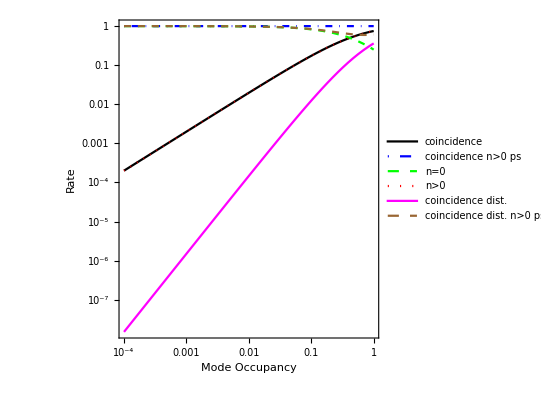

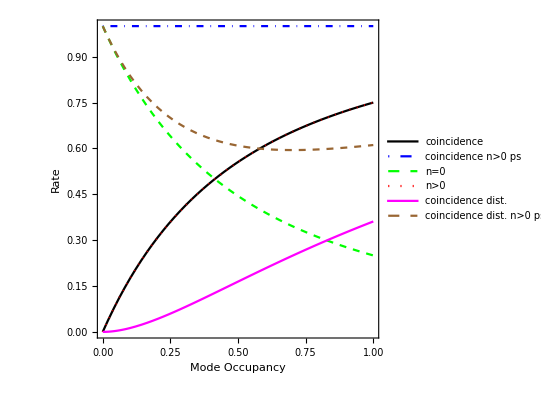

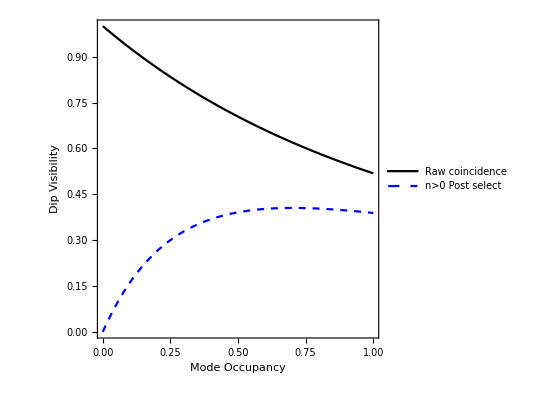

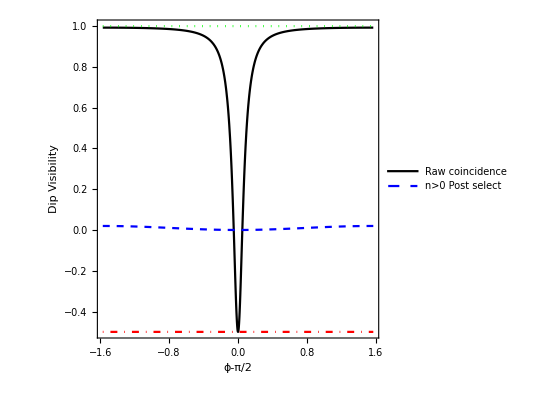

```mathematica
phiTemp=0

LogLogPlot[
{1-ClickNcoProb/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProb-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ClickNcoProbDist/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProbDist-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp}
}
,{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},
Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]

Plot[
{1-ClickNcoProb/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProb-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ProbNoAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-ClickNcoProbDist/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
1-(ClickNcoProbDist-ProbNoAtoms)/.{λ->lambdaGivenN[x],ϕ-> phiTemp}
}
,{x,1,10^-4},AspectRatio->1,PlotLegends->Placed[{"coincidence","coincidence n>0 ps","n=0","n>0 ","coincidence dist.","coincidence dist. n>0 ps"},Top],PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},
Frame->True,FrameLabel->{"Mode Occupancy","Rate"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]

Plot[{
HOMClickClickDipVisibility/.{λ->lambdaGivenN[x],ϕ-> phiTemp},
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[x],ϕ-> phiTemp}}
,{x,1,10^-6},AspectRatio->1,PlotLegends->Placed[{"Raw coincidence","n>0 Post select"},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"Mode Occupancy","Dip Visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
λtmp=0.01;
Plot[{
HOMClickClickDipVisibility/.{λ->lambdaGivenN[λtmp],ϕ-> ϕplot-π/2},
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[λtmp],ϕ-> ϕplot-π/2},
1,-0.5}
,{ϕplot,-π/2,π/2},AspectRatio->1,PlotLegends->Placed[{"Raw coincidence","n>0 Post select"},Top],PlotStyle->{{Black},{Blue,Dashed},{Green,Dotted},{Red,DotDashed}},Frame->True,FrameLabel->{"ϕ-π/2","Dip Visibility"},BaseStyle->{FontSize->12,FontColor->Black}]
```

```mathematica
HOMClickClickDipVisibilityPs1orMoreAtoms/.{λ->lambdaGivenN[0.001],ϕ-> 0.1}
```

0.00197567

```mathematica
HOMClickClickDipVisibility/.{λ->lambdaGivenN[0.001],ϕ-> 0.1}
```

0.999243

## Colinear g2

```mathematica
Solve[m+n-j-k-W==0 &&j+k-X==0 &&m+n-a-b-Y==0 &&a+b-Z==0]
```

{{W→-j-k+m+n,X→j+k,Y→-a-b+m+n,Z→a+b}}

```mathematica
ProbWXYZV1[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=Abs[(1-λin^2)ParallelSum[λin^(m+n)1/(Factorial[m]Factorial[n])(1/2)^(m+n)ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-j+k)ⅇ^(ⅈ ϕin(-j-k))
					Binomial[m,j]Binomial[n,k]
					√(Factorial[m+n-j-k]Factorial[j+k])
					)
				(ⅈ^(-a+b)ⅇ^(ⅈ ϕin(-a-b))
					Binomial[m,a]Binomial[n,b] 
					√(Factorial[m+n-a-b]Factorial[a+b])
					
					)KroneckerDelta[m+n-j-k-Win]KroneckerDelta[j+k-Xin]KroneckerDelta[m+n-a-b-Yin]KroneckerDelta[a+b-Zin] 
,{m,0,Win+Xin},{n,0,Win+Xin},{j,0,m},{k,0,n},{a,0,m},{b,0,n}]]^2
tablethinkg=ProbWXYZV1[1,4,2,3,0.1,π/4]

Table[ProbWXYZV1[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV1[1,4,2,3,0.1,π/4],ProbWXYZV1[0,2,2,0,0.1,0],ProbWXYZV1[1,1,2,0,0.1,0],ProbWXYZV1[2,0,2,0,0.1,π/4]}
```

6.12562×10^-12

{0.,0.,1.22512×10^-11,0.,0.,0.}

{6.12562×10^-12,0.00009801,0.,0.0000245025}

```mathematica
ProbWXYZV2[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=Abs[(1-λin^2)ParallelSum[λin^(m+(Win+Xin-m))1/(Factorial[m]Factorial[(Win+Xin-m)])(1/2)^(m+(Win+Xin-m))ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-j+k)ⅇ^(ⅈ ϕin(-j-k))
					Binomial[m,j]Binomial[(Win+Xin-m),k]
					√(Factorial[m+(Win+Xin-m)-j-k]Factorial[j+k])
					
					)
				(ⅈ^(-a+b)ⅇ^(ⅈ ϕin(-a-b))
					Binomial[m,a]Binomial[(Win+Xin-m),b] 
					√(Factorial[m+(Win+Xin-m)-a-b]Factorial[a+b])
					
					)KroneckerDelta[m+(Win+Xin-m)-j-k-Win]KroneckerDelta[j+k-Xin]KroneckerDelta[(Win+Xin)-Zin-Yin]KroneckerDelta[a+b-Zin] 
,{m,0,Win+Xin},{j,0,m},{k,0,(Win+Xin-m)},{a,0,m},{b,0,(Win+Xin-m)}]]^2
Table[ProbWXYZV2[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV2[1,4,2,3,0.1,π/4],ProbWXYZV2[0,2,2,0,0.1,0],ProbWXYZV2[1,1,2,0,0.1,0],ProbWXYZV2[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22512×10^-11,0.,0.,0.}

{6.12562×10^-12,0.00009801,0.,0.0000245025}

```mathematica
g2inhalo=(2 ParallelSum[ProbWXYZV2[2,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV2[1,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}]+2ParallelSum[ProbWXYZV2[2,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}])^2
g2xhalo=(ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,0 π/2]X W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,0 π/2]W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}]
ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,0 π/2]X,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])
g2xhalo=(ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,π/2]X W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,π/2]W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}]
ParallelSum[ProbWXYZV2[W,X,Y,Z,0.01,π/2]X,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])
```

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.9994

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.

```mathematica
Binomial[2,3]
```

0

```mathematica
ProbWXYZV3[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=KroneckerDelta[(Win+Xin)-Zin-Yin] Abs[(1-λin^2)ParallelSum[λin^(m+(Win+Xin-m))1/(Factorial[m]Factorial[(Win+Xin-m)])(1/2)^(m+(Win+Xin-m))ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-j+(Xin-j))ⅇ^(ⅈ ϕin(-j-(Xin-j)))
					Binomial[m,j]Binomial[(Win+Xin-m),(Xin-j)]
					√(Factorial[m+(Win+Xin-m)-j-(Xin-j)]Factorial[j+(Xin-j)])
					
					)
				(ⅈ^(-a+(Zin-a))ⅇ^(ⅈ ϕin(-a-(Zin-a)))
					Binomial[m,a]Binomial[(Win+Xin-m),Zin-a] 
					√(Factorial[m+(Win+Xin-m)-a-(Zin-a)]Factorial[a+Zin-a])
					
					)KroneckerDelta[m+(Win+Xin-m)-j-(Xin-j)-Win]KroneckerDelta[j+(Xin-j)-Xin]KroneckerDelta[(Win+Xin)-Zin-Yin]KroneckerDelta[a+Zin-a-Zin] 
,{m,0,Win+Xin},{j,0Max[0,m-Win],Min[m,Xin]},{a,0,Min[m,Zin]}]]^2
Table[ProbWXYZV3[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV3[1,4,2,3,0.1,π/4],ProbWXYZV3[0,2,2,0,0.1,0],ProbWXYZV3[1,1,2,0,0.1,0],ProbWXYZV3[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22512×10^-11,0.,0.,0.}

{6.12562×10^-12,0.00009801,0.,0.0000245025}

```mathematica
ProbWXYZV4[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=Abs[(1-λin^2)
√(Factorial[Win+Xin-Zin]Factorial[Zin])√(Factorial[Win+Xin-Xin]Factorial[Xin])ⅈ^(2 Xin)
ParallelSum[λin^(m+(Win+Xin-m))1/(Factorial[m]Factorial[(Win+Xin-m)])(1/2)^(m+(Win+Xin-m))ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-2j)ⅇ^(ⅈ ϕin(-Xin))
					Binomial[m,j]Binomial[Win+Xin-m,(Xin-j)]
					
					)
				(ⅈ^(-2a+Zin)ⅇ^(ⅈ ϕin(-Zin))
					Binomial[m,a]Binomial[Win+Xin-m,(Zin-a)] 
					
					
					)KroneckerDelta[(Win+Xin)-Zin-Yin]
,{m,0,Win+Xin},{j,0,m},{a,0,m}]]^2
Table[ProbWXYZV4[win,3,2,3,0.1,π/4],{win,0,5}]
Table[ProbWXYZV4[win,2,2,3,0.1,π/4],{win,0,5}]
Table[ProbWXYZV4[win,3,2,2,0.1,π/4],{win,0,5}]
```

{0.,0.,1.22512×10^-11,0.,0.,0.}

Infinity::indet: Indeterminate expression 0. √2 ComplexInfinity encountered.

{Indeterminate,0.,0.,1.22513×10^-11,0.,0.}

{0.,0.,0.,0.,0.,0.}

```mathematica
Table[ProbWXYZV3[2,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,2},{Z,0,3}]
```

Infinity::indet: Indeterminate expression 0 ⅇ^(-(3 ⅈ π)/4) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ⅇ^(-(3 ⅈ π)/4) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ⅇ^(-(3 ⅈ π)/4) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{0.,0.,2.4995×10^-9,Indeterminate},{0.,4.999×10^-9,0.,Indeterminate},{2.4995×10^-9,0.,0.,Indeterminate}},{{0.,0.,0.,3.74925×10^-13},{0.,0.,1.24975×10^-13,0.},{0.,1.24975×10^-13,0.,0.}},{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,2.4995×10^-17,0.}},{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.24975×10^-21}}}

```mathematica
g2inhalo=(2 ParallelSum[ProbWXYZV3[2,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV3[1,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}]+2ParallelSum[ProbWXYZV3[2,X,Y,Z,0.01,π/4],{X,0,3},{Y,0,3},{Z,0,3}])^2
g2xhalo=(ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,0 π/2]X W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,0 π/2]W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}]
ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,0 π/2]X,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])
g2xhalo=(ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,π/2]X W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])/(ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,π/2]W,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}]
ParallelSum[ProbWXYZV3[W,X,Y,Z,0.01,π/2]X,{W,0,3},{X,0,3},{Y,0,3},{Z,0,3}])
```

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.9994

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

ParallelSum::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelSum::subpar will be suppressed during this calculation.

1.

```mathematica
ProbWXYZV4[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=Abs[(1-λin^2)
√(Factorial[Win+Xin-Zin]Factorial[Zin])√(Factorial[Win+Xin-Xin]Factorial[Xin])ⅈ^Xin ⅈ^Zin
NSum[λin^(m+(Win+Xin-m))1/(Factorial[m]Factorial[(Win+Xin-m)])(1/2)^(m+(Win+Xin-m))ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
				(ⅈ^(-2j)ⅇ^(ⅈ ϕin(-Xin))
					Binomial[m,j]Binomial[Win+Xin-m,(Xin-j)]
					
					)
				(ⅈ^(-2a)ⅇ^(ⅈ ϕin(-Zin))
					Binomial[m,a]Binomial[Win+Xin-m,(Zin-a)] 
					)KroneckerDelta[(Win+Xin)-Zin-Yin]
,{m,0,Win+Xin},{j,0,m},{a,0,m}]]^2
Table[ProbWXYZV4[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV4[1,4,2,3,0.1,π/4],ProbWXYZV4[0,2,2,0,0.1,0],ProbWXYZV4[1,1,2,0,0.1,0],ProbWXYZV4[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22513×10^-11,0.,0.,0.}

{6.12563×10^-12,0.00009801,0.,0.0000245025}

```mathematica
Sum[ⅈ^(-2j)Binomial[m,j]Binomial[Win+Xin-m,(Xin-j)]
,{j,0,m}]
```

Binomial[-m+Win+Xin,Xin] Hypergeometric2F1[-m,-Xin,1-m+Win,-1]

```mathematica
ProbWXYZV5[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=KroneckerDelta[(Win+Xin)-Zin-Yin] *
Abs[(1-λin^2)
	√(Factorial[Win+Xin-Zin]Factorial[Zin])√(Factorial[Win+Xin-Xin]Factorial[Xin])ⅈ^Xin ⅈ^Zin
	(1/2)^(Win+Xin)ⅇ^(ⅈ ϕin(-Xin))ⅇ^(ⅈ ϕin(-Zin))λin^(Win+Xin)
NSum[1/(Factorial[m]Factorial[(Win+Xin-m)])ⅈ^(2m)ⅇ^(ⅈ ϕin(2m))
			Sum[(-1)^j Binomial[m,j]Binomial[Win+Xin-m,(Xin-j)]
			,{j,0,m}]
			Sum[(-1)^a Binomial[m,a]Binomial[Win+Xin-m,(Zin-a)] 
			,{a,0,m}]
,{m,0,Win+Xin}]
]^2
Table[ProbWXYZV5[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV5[1,4,2,3,0.1,π/4],ProbWXYZV5[0,2,2,0,0.1,0],ProbWXYZV5[1,1,2,0,0.1,0],ProbWXYZV5[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22512×10^-11,0.,0.,0.}

{6.12563×10^-12,0.00009801,0.,0.0000245025}

```mathematica
λtmp=0.001
normtmp=ProbWXYZV5[1,1,1,1,λtmp,0];
Table[ProbWXYZV5[win,3,2,3,λtmp,π/4],{win,0,5}] normtmp^-1
Print["11 case"]
Table[ProbWXYZV5[win,2-win,1,1,λtmp,0],{win,0,2}] normtmp^-1
Table[ProbWXYZV5[win,2-win,1,1,λtmp,1 π/2],{win,0,2}] normtmp^-1
Print["20 case"]
Table[ProbWXYZV5[win,2-win,2,0,λtmp,0],{win,0,2}] normtmp^-1
Table[ProbWXYZV5[win,2-win,2,0,λtmp,π/2],{win,0,2}] normtmp^-1
Table[ProbWXYZV5[win,2-win,2,0,λtmp,π/4],{win,0,2}] normtmp^-1
Table[ProbWXYZV5[win,4,2,2,λtmp,π/4],{win,0,5}] normtmp^-1
```

0.001

{0.,0.,1.25×10^-19,0.,0.,0.}

11 case

{0.,1.,0.}

{0.,1.,0.}

20 case

{1.,0.,0.}

{0.,0.,1.}

{0.25,0.5,0.25}

{3.75×10^-13,0.,0.,0.,0.,0.}

```mathematica
ProbWXYZV5[1,X,Y,Z,0.1,π/4]
```

```mathematica
g2xhalo=ParallelSum[ProbWXYZV5[1,X,Y,Z,0.1,π/4]X,{X,1,2},{Y,1,3},{Z,1,3}]
```

Infinity::indet: Indeterminate expression 0. ⅇ^(-(ⅈ π)/4) ⅇ^(-(3 ⅈ π)/4) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
FullSimplify[FunctionExpand[(-1)^j Binomial[m,j]Binomial[Win+Xin-m,(Xin-j)],{Assumptions->{Win,Xin,j,m}∈Integers,{Win,Xin,j,m}≥0 }],,Assumptions->{{Win,Xin,j,m}∈Integers,{Win,Xin,j,m}≥0 }]
```

((-1)^j Gamma[1+m] Gamma[1-m+Win+Xin])/(Gamma[1+j] Gamma[1-j+m] Gamma[1+j-m+Win] Gamma[1-j+Xin])

```mathematica
FullSimplify[FunctionExpand[(-1)^a Binomial[m,a]Binomial[Win+Xin-m,(Z-a)],{Assumptions->{Win,Xin,j,m}∈Integers,{Win,Xin,j,m}≥0 }],,Assumptions->{{Win,Xin,j,m}∈Integers,{Win,Xin,j,m}≥0 }]
```

((-1)^a Gamma[1+m] Gamma[1-m+Win+Xin])/(Gamma[1+a] Gamma[1-a+m] Gamma[1+a-m+Win+Xin-Z] Gamma[1-a+Z])

```mathematica
CleanInnerSumExpansionA[Win_,Xin_,m_,j_]=((-1)^j Factorial[m] Factorial[-m+Win+Xin])/(Factorial[j] Factorial[-j+m] Factorial[+j-m+Win] Factorial[-j+Xin])
```

((-1)^j m! (-m+Win+Xin)!)/(j! (-j+m)! (j-m+Win)! (-j+Xin)!)

```mathematica
CleanInnerSumExpansionB=((-1)^a Factorial[m] Factorial[-m+Win+Xin])/(Factorial[a] Factorial[-a+m] Factorial[+a-m+Win+Xin-Z] Factorial[-a+Z])
```

((-1)^a m! (-m+Win+Xin)!)/(a! (-a+m)! (a-m+Win+Xin-Z)! (-a+Z)!)

```mathematica
InnerSymSumA[Win_,Xin_,m_]=FullSimplify[
Sum[
	((-1)^j Factorial[m] Factorial[-m+Win+Xin])/(Factorial[j] Factorial[-j+m] Factorial[+j-m+Win] Factorial[-j+Xin])
,{j,0,m},
Assumptions->{Win∈Integers,Xin∈Integers,j∈Integers,m∈Integers,{Win,Xin,j,m}≥0 }]
,Assumptions->{Win∈Integers,Xin∈Integers,j∈Integers,m∈Integers,{Win,Xin,j,m}≥0 }
]
InnerNumSumA[Win_,Xin_,Min_]:=Sum[(-1)^j Binomial[Min,j]Binomial[Win+Xin-Min,(Xin-j)]
			,{j,0,Min}]
InnerNumTotalA[Win_,Xin_,Min_]:=Total[Table[(-1)^j Binomial[Min,j]Binomial[Win+Xin-Min,(Xin-j)]
			,{j,0,Min}]]
Table[InnerSymSumA[2,1,m],{m,0,5}]
Table[InnerNumSumA[2,1,m],{m,0,5}]
Table[InnerNumTotalA[2,1,m],{m,0,5}]
```

(Gamma[1-m+Win+Xin] Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/Gamma[1+Xin]

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{3,1,-1,-3,Indeterminate,Indeterminate}

{3,1,-1,-3,6,-30}

{3,1,-1,-3,6,-30}

```mathematica
InnerSymSumB[Win_,Xin_,m_]=FullSimplify[
Sum[
((-1)^a m! (-m+Win+Xin)!)/(a! (-a+m)! (a-m+Win+Xin-Z)! (-a+Z)!)
,{a,0,m},
Assumptions->{Win∈Integers,Xin∈Integers,j∈Integers,m∈Integers,{Win,Xin,j,m}≥0 }]
,Assumptions->{Win∈Integers,Xin∈Integers,j∈Integers,m∈Integers,{Win,Xin,j,m}≥0 }
]
```

(Gamma[1-m+Win+Xin] Hypergeometric2F1Regularized[-m,-Z,1-m+Win+Xin-Z,-1])/Gamma[1+Z]

```mathematica
InnerSymSumCleanA[Win_,Xin_,m_]=(Factorial[-m+Win+Xin] Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/Factorial[Xin]
Table[InnerSymSumCleanA[2,1,m],{m,0,5}]
```

((-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/(Xin!)

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{3,1,-1,-3,Indeterminate,Indeterminate}

```mathematica
InnerSymSumCleanB[Win_,Xin_,Zin_,m_]=(Factorial[-m+Win+Xin]Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1])/Factorial[+Zin]
```

((-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1])/(Zin!)

```mathematica
((-m+Win+Xin)! Hypergeometric2F1[-m,-Xin,1-m+Win,-1])/(Xin!Gamma[1-m+Win])
```

((-m+Win+Xin)! Hypergeometric2F1[-m,-Xin,1-m+Win,-1])/(Xin! Gamma[1-m+Win])

```mathematica
FunctionExpand[Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1]]
```

Hypergeometric2F1[-m,-Xin,1-m+Win,-1]/Gamma[1-m+Win]

```mathematica
InnerSymSumCleanCleanA[Win_,Xin_,m_]=(Factorial[-m+Win+Xin] Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/Factorial[Xin]
Table[InnerSymSumCleanA[0,1,m],{m,0,3}]
```

((-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/(Xin!)

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{1,-1,Indeterminate,Indeterminate}

```mathematica
InnerSymSumCleanCleanA[Win_,Xin_,m_]=((-m+Win+Xin)!)/(Xin!) (Gamma[1-m+Xin]Gamma[1-1/2 m])/(Gamma[1-m]Gamma[1-1/2 m+Xin])
Table[InnerSymSumCleanA[2,1,m],{m,0,5}]
```

((-m+Win+Xin)! Gamma[1-m/2] Gamma[1-m+Xin])/(Xin! Gamma[1-m] Gamma[1-m/2+Xin])

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{3,1,-1,-3,Indeterminate,Indeterminate}

((-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1])/((1+Xin)!)

```mathematica
ProbWXYZV6[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=KroneckerDelta[(Win+Xin)-Zin-Yin] *
Abs[(1-λin^2)
	√(Factorial[Win+Xin-Zin]Factorial[Zin])√(Factorial[Win+Xin-Xin]Factorial[Xin])ⅈ^Xin ⅈ^Zin
	(1/2)^(Win+Xin)ⅇ^(ⅈ ϕin(-Xin))ⅇ^(ⅈ ϕin(-Zin))λin^(Win+Xin)
Sum[1/(Factorial[m]Factorial[(Win+Xin-m)])(-1)^m ⅇ^(ⅈ ϕin(2m))
			InnerSymSumCleanA[Win,Xin,m]
		InnerSymSumCleanB[Win,Xin,Zin,m]
,{m,0,Win+Xin}]
]^2
Table[ProbWXYZV6[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV6[1,4,2,3,0.1,π/4],ProbWXYZV6[0,2,2,0,0.1,0],ProbWXYZV6[1,1,2,0,0.1,0],ProbWXYZV6[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22513×10^-11,0.,0.,0.}

{6.12563×10^-12,0.00009801,0.,0.0000245025}

```mathematica
1/(Factorial[m]Factorial[(Win+Xin-m)])(-1)^m ⅇ^(ⅈ ϕin(2m))
			InnerSymSumCleanA[Win,Xin,m]
			InnerSymSumCleanB[Win,Xin,Zin,m]
```

((-1)^m ⅇ^(2 ⅈ m ϕin) (-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1] Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1])/(m! Xin! Zin!)

```mathematica
FullSimplify[ExpandAll[1/(Factorial[m]Factorial[(Win+Xin-m)])(-1)^m ⅇ^(ⅈ ϕin(2m))
			InnerSymSumCleanA[Win,Xin,m]
			InnerSymSumCleanB[Win,Xin,Zin,m]
]
,Assumptions->{Win∈Integers,Xin∈Integers,m∈Integers,Win≥0 ,Xin≥0 ,Win≥0,m≥0  }]
```

((-1)^m ⅇ^(2 ⅈ m ϕin) (-m+Win+Xin)! Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1] Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1])/(m! Xin! Zin!)

```mathematica
ProbWXYZV7[Win_,Xin_,Yin_,Zin_,λin_,ϕin_]:=KroneckerDelta[(Win+Xin)-Zin-Yin] *
(Factorial[Yin]Factorial[Win])/(Factorial[Xin] Factorial[Zin])(1-λin^2)^2(1/2)^(2(Win+Xin))λin^(2(Win+Xin))Abs[
ParallelSum[
(-1)^m ⅇ^(2 ⅈ m ϕin) ((-m+Win+Xin)!)/(m!) Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1] Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1]
,{m,0,Win+Xin}]
]^2
Table[ProbWXYZV7[win,3,2,3,0.1,π/4],{win,0,5}]
{ProbWXYZV7[1,4,2,3,0.1,π/4],ProbWXYZV7[0,2,2,0,0.1,0],ProbWXYZV7[1,1,2,0,0.1,0],ProbWXYZV7[2,0,2,0,0.1,π/4]}
```

{0.,0.,1.22513×10^-11,0.,0.,0.}

{6.12563×10^-12,0.00009801,0.,0.0000245025}

```mathematica
KroneckerDelta[(Win+Xin)-Zin-Yin]
```

```mathematica
((-m+Win+Xin)!)/(m!)(-1)^m ⅇ^(2 ⅈ m ϕin)  Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1] Hypergeometric2F1Regularized[-m,-Zin,1-m+Yin,-1]/.{ϕin->0,Win->1,Xin->1,Zin->1,Yin->1}
```

(4 (-1)^m (-1+m)^2 (2-m)!)/((-2+m)^2 m! Gamma[2-m]^2)

```mathematica
Table[
(-1)^m ⅇ^(2 ⅈ m ϕin) ((-m+Win+Xin)!)/(m!) Hypergeometric2F1Regularized[-m,-Xin,1-m+Win,-1] Hypergeometric2F1Regularized[-m,-Zin,1-m+Win+Xin-Zin,-1]
,{m,0,1}]/.{ϕin->0,Win->1,Xin->1,Zin->1,Yin->1}
```

{2,0}

## Postselection

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[probnm[n,m]probncoNM[n,m] KroneckerDelta[n+m-t],{n,1,t},{m,1,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t≥ 2}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoDistNtot=FullSimplify[Sum[((1-λ^2)(λ^t))^2*2*(1/2)^t,{n,2,t}]+ 2*((1-λ^2)(λ^t))^2 2*(1/2)^t,Assumptions->{λ∈Reals,λ>0,t>0}]
```

2^(1-t) (1+t) λ^(2 t) (-1+λ^2)^2

```mathematica
ProbNcoIndistNtot=2 ( ( 1-λ^2) λ^t)^2
```

2 λ^(2 t) (1-λ^2)^2

```mathematica
visbPostSelNtot=FullSimplify[((1-ProbNcoDistNtot)-(1-ProbNcoIndistNtot))/(1-ProbNcoDistNtot),Assumptions->{λ∈Reals,λ>0,λ<1(*,t>0*)}]
```

-(2 (-1+2^t-t) λ^(2 t) (-1+λ^2)^2)/(-2^t+2 (1+t) λ^(2 t) (-1+λ^2)^2)

```mathematica
visbPostSelNtot/.{t->2,λ->0.5}
```

0.0185567

```mathematica
visbPostSelNtot/.{t->3,λ->Abs[lambdaGivenN[0.9]]}
```

0.0303346

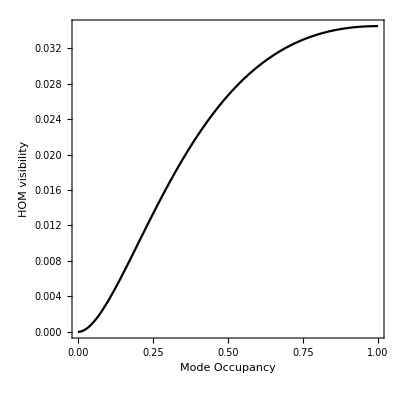

```mathematica
Plot[{visbPostSelNtot/.{λ->Abs[lambdaGivenN[x]],t->2}},{x,1,10^-4},AspectRatio->1,PlotStyle->{{Black},{Blue,DotDashed},{Green,Dashed},{Red,Dotted},{Magenta},{Brown,Dashed}},Frame->True,FrameLabel->{"Mode Occupancy","HOM visibility"},BaseStyle->{FontSize->12,FontColor->Black},AxesStyle->{Thick,Black}]
```

### Coin flipping

```mathematica
NHeadsChance[n_,h_]=(1/2)^n Binomial[n,h]
```

2^-n Binomial[n,h]

Plot::plln: Limiting value n in {x,0,n} is not a machine-sized real number.

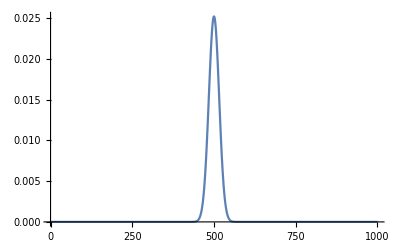

```mathematica
Plot[NHeadsChance[n,x],{x,0,n},PlotRange->All]/.{n->1000}
```